```mathematica
borelZ[λ_]=Sqrt[Pi] Sum[((4k)!(-1)^k)/(2^(4k)(2k)!k!k!)λ^k,{k,0,Infinity}]
```

(2 EllipticK[(-1+√(1+4 λ))/(2 √(1+4 λ))])/(√π (1+4 λ)^(1/4))

```mathematica
borelZ[λ]
```

(2 EllipticK[(-1+√(1+4 λ))/(2 √(1+4 λ))])/(√π (1+4 λ)^(1/4))

```mathematica
borelZ[1]//N
```

1.28306

```mathematica
borelZ[0]
```

√π

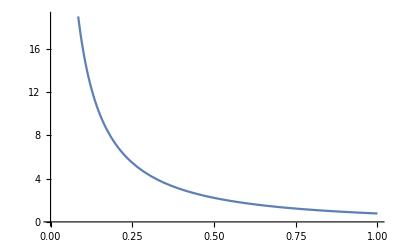

```mathematica
Plot[Exp[-λ / 2]borelZ[λ]//N, {λ,0,1}]
```

```mathematica
laplaceborelZ[z_] = Integrate[Exp[-λ]borelZ[z λ], {λ,0,Infinity}]
```

∫_0^∞ (2 ⅇ^-λ EllipticK[(-1+√(1+4 z λ))/(2 √(1+4 z λ))])/(√π (1+4 z λ)^(1/4))ⅆλ

```mathematica
Integrate[Exp[-λ]borelZ[0 λ], {λ,0,Infinity}]
```

√π

```mathematica
f[z_] :=NIntegrate[Exp[- λ]borelZ[z λ], {λ,0,Infinity}]
```

```mathematica
f[0]
```

1.77245

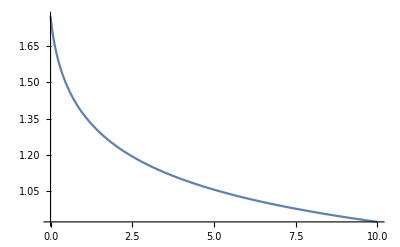

```mathematica
Plot[f[z],{z,0,10}]
```

```mathematica
analyticSolution[λ_] := (Exp[-1/(8λ)] BesselK[1/4, 1/(8λ)])/(2Sqrt[λ])
```

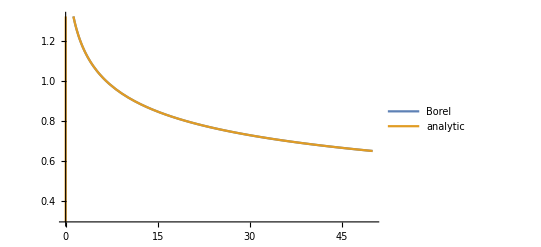

```mathematica
Plot[{f[z], analyticSolution2[z]},{z,0,50}, PlotLegends->{"Borel", "analytic"}]
```

```mathematica
analyticSolution2[λ_]=Normal[Integrate[Exp[-x^2-λ x^4], {x,-Infinity, Infinity}]]
```

(ⅇ^(1/8/λ) BesselK[1/4,1/(8 λ)])/(2 √λ)

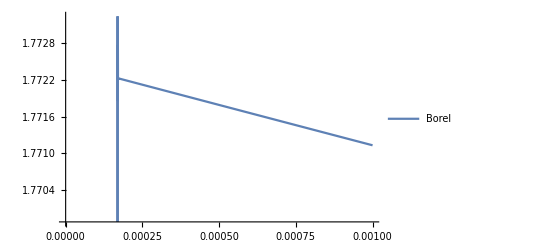

```mathematica
Plot[analyticSolution2[z],{z,0,0.001}, PlotLegends->{"Borel", "analytic"}]
```

```mathematica
Limit[analyticSolution2[z], {z->0}]
```

Indeterminate

```mathematica
analyticSolution2[0.001]
```

1.77113

```mathematica
Series[analyticSolution2[z], {z,0,5}]
```

(-1)^Floor[(π+Arg[z])/(2 π)] (√π-(3 √π z)/4+(105 √π z^2)/32-(3465 √π z^3)/128+(675675 √π z^4)/2048-(43648605 √π z^5)/8192+O[z]^6)

```mathematica
asymptSeries[λ_, n_] := Sum[Sqrt[Pi] ((-λ)^k(4k)!)/(2^(4k)(2k)!k!), {k,0,n}]
```

```mathematica
asymptSeries[λ, 5]
```

√π-(3 √π λ)/4+(105 √π λ^2)/32-(3465 √π λ^3)/128+(675675 √π λ^4)/2048-(43648605 √π λ^5)/8192

```mathematica
Series[Exp[1/(8λ)], {λ, 0, 5}]
```

ⅇ^(1/(8 λ)+O[λ]^6)

## Other Borel Definition

```mathematica
borelZ2[λ_]=Sqrt[Pi] Sum[((4k)!(-1)^k)/(2^(4k)(2k)!k!(k-1)!)λ^(k-1),{k,0,Infinity}]
```

-3/4 √π Hypergeometric2F1[5/4,7/4,2,-4 λ]

```mathematica
-3/4 √π Hypergeometric2F1[5/4,7/4,2,-4 λ]//Simplify
```

-3/4 √π Hypergeometric2F1[5/4,7/4,2,-4 λ]

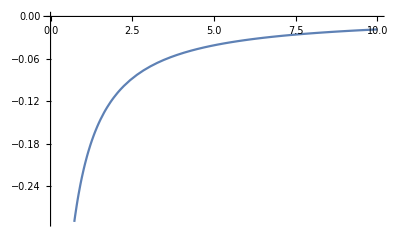

```mathematica
Plot[borelZ2[λ], {λ,0,10}]
```

```mathematica
Integrate[borelZ2[λ]Exp[-z λ], {λ,0,Infinity}]
```

ConditionalExpression[-3/4 √π (4/3-(2 ⅇ^(z/8) √z BesselK[-1/4,z/8])/(3 √π)), Re[z]>0]

```mathematica
-3/4 √π (4/3-(2 ⅇ^(z/8) √z BesselK[-1/4,z/8])/(3 √π))/.{z->1/λ}//FullSimplify
```

-√π+1/2 ⅇ^(1/8/λ) √(1/λ) BesselK[1/4,1/(8 λ)]

```mathematica
Sqrt[Pi] Sum[((4k)!(-1)^k)/(2^(4k)(2k)!k!(k-1)!)λ^(k-1),{k,1,Infinity}]
```

-3/4 √π Hypergeometric2F1[5/4,7/4,2,-4 λ]

```mathematica
((4k)!(-1)^k)/(2^(4k)(2k)!k!(k-1)!)λ^(k-1)/.{k->0}
```

0